## Basic Data Visualization of Sheep paddock

```mathematica
rawMetadata=Import["/Users/katjad/Documents/Github/SheepCapstone/Salt6_corners_food locations_collective decision making_March2019.csv"];
```

```mathematica
Grid[rawMetadata,Frame->All];
```

```mathematica
paddock=rawMetadata[[-4;;-1,-2;;-1]];
feeding=rawMetadata[[2;;11,-2;;-1]];
water=rawMetadata[[12,-2;;-1]];
```

Boundary Graphic for use in later plots

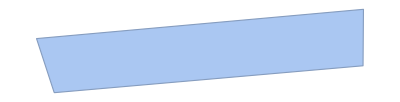

```mathematica
paddockRegion=BoundaryDiscretizeGraphics[Polygon[paddock]]
```

Background Graphic of the sheep paddock including water and food stations

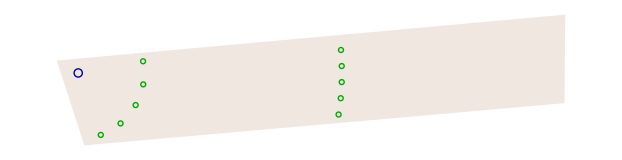

```mathematica
metadataGraphic=Graphics[{LightBrown,Polygon[paddock],Darker[Green],Circle[#,30]&/@feeding,Thick,Darker[Blue],Circle[water,50]}]
```

## Basic Visualizations of sheep movement

```mathematica
rawXs=Import["/Users/katjad/Documents/Github/SheepCapstone/xs.csv"];
rawYs=Import["/Users/katjad/Documents/Github/SheepCapstone/ys.csv"];
rawIDs=Import["/Users/katjad/Documents/Github/SheepCapstone/ids.csv"];
rawTs=Import["/Users/katjad/Documents/Github/SheepCapstone/ts.csv"];
rawTsStart=Import["/Users/katjad/Documents/Github/SheepCapstone/period.start.idxs.csv"];
```

```mathematica
Dimensions[rawXs]
```

{52,210352}

```mathematica
rawYs[[2]]
```

{1,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,210326,6.56366×10^6,6.56366×10^6,6.56367×10^6,6.56367×10^6,6.56367×10^6,6.56367×10^6,6.56367×10^6,6.56367×10^6,6.56368×10^6,6.56368×10^6,6.56368×10^6,6.56368×10^6,NA}
 |  |  |  |

```mathematica
rawCoordinates=Table[{rawXs[[x,y]],rawYs[[x,y]]},{x,2,52},{y,2,210352}]/."NA"->Missing[];
```

#### Path of Sample Sheep

```mathematica
Grid[{#,Show[metadataGraphic,Graphics[{Thin,Line[DeleteMissing[rawCoordinates[[#]],1,2]]}]]}&/@RandomSample[Range[51],5]]
```

2 | -Graphics-
9 | -Graphics-
44 | -Graphics-
51 | -Graphics-
29 | -Graphics-

#### X-coordinate correlation

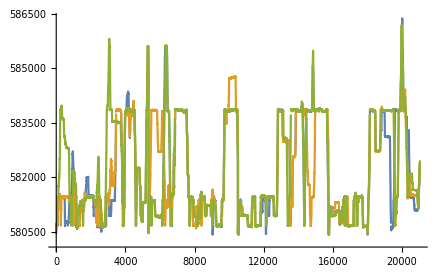

```mathematica
ListLinePlot[rawCoordinates[[{3,9,44},;;;;10,1]]]
```

```mathematica
ListLinePlot[rawCoordinates[[All,;;;;50,1]],Frame->True,FrameLabel->{Style["Data point(~time)",Large],Style["x-coordinate",Large]}]
```

```mathematica
sheep51=DeleteMissing[rawCoordinates[[51]],1,2];
```

```mathematica
rasterizedSheep51graphic=Rasterize[sheep51graphic]
```

-Graphics-

```mathematica
Rasterize[sheep51graphic,"BoundingBox"]
```

{360,104,55}

```mathematica
sheep51[[1]]
```

{580426.,6.56368×10^6}

```mathematica
Inset
```

```mathematica
Manipulate[Show[rasterizedSheep51graphic,Graphics[Circle[sheep51[[n]],100]]],{n,1,Length[sheep51],1}]
```

Part::partd: Part specification sheep51⟦95692⟧ is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in Show[rasterizedSheep51graphic,].

#### Density Plot

```mathematica
Show[metadataGraphic,Graphics[{Thin,Line[DeleteMissing[#,1,2]]&/@rawCoordinates}]]
```

$Aborted[]

#### Density Plot

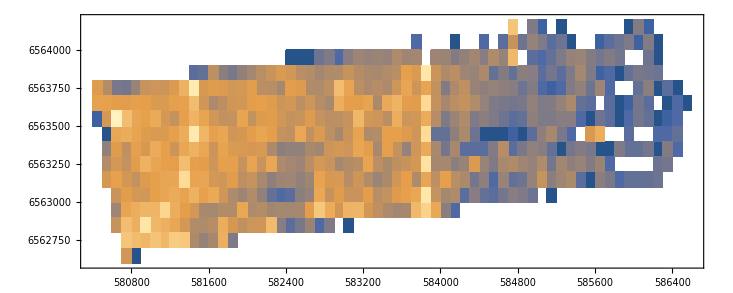

```mathematica
DensityHistogram[RandomSample[Catenate[rawCoordinates],100000],{{100},{100}},{"Log","PDF"},AspectRatio->Automatic]
```

## Conversion to time series

### Testing

```mathematica
times=rawTs[[2;;,2]];
```

```mathematica
FromUnixTime[times[[2]]]
```

Thu 29 Nov 2018 00:43:25GMT-4.

```mathematica
unixTimes=FromUnixTime/@times;
```

```mathematica
rawXs[[2]]
```

```mathematica
Length[rawXs[[2,2;;]]]
```

210351

```mathematica
Length[unixTimes]
```

210351

```mathematica
testTS2=TimeSeries[rawXs[[2,2;;]]/."NA"->Missing[],{unixTimes},MissingDataMethod->None]
```

TemporalData[TimeSeries, <<1>>]

```mathematica
testTS9=TimeSeries[rawXs[[9,2;;]]/."NA"->Missing[],{unixTimes},MissingDataMethod->None]
```

TemporalData[TimeSeries, <<1>>]

```mathematica
testTS44=TimeSeries[rawXs[[44,2;;]]/."NA"->Missing[],{unixTimes},MissingDataMethod->None]
```

TemporalData[TimeSeries, <<1>>]

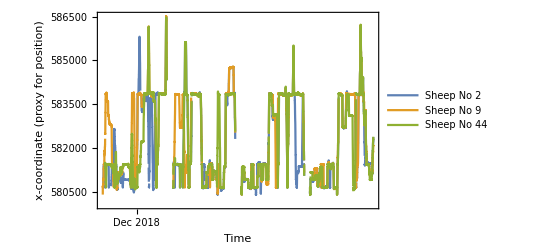

```mathematica
DateListPlot[{TimeSeriesResample[testTS2,"Minute"],TimeSeriesResample[testTS9,"Minute"],TimeSeriesResample[testTS44,"Minute"]},Frame->True,FrameLabel->{"Time","x-coordinate (proxy for position)"},PlotLegends->{"Sheep No 2","Sheep No 9","Sheep No 44"}]
```

```mathematica
rawTs
```

{{,x},{1,1543466599},{2,1543466605},{3,1543466611},{4,1543466617},{5,1543466623},{6,1543466629},{7,1543466635},{8,1543466641},{9,1543466647},{10,1543466653},{11,1543466659},{12,1543466665},{13,1543466671},{14,1543466677},{15,1543466683},{16,1543466689},210318,{210335,1544821104},{210336,1544821110},{210337,1544821116},{210338,1544821122},{210339,1544821128},{210340,1544821134},{210341,1544821140},{210342,1544821146},{210343,1544821152},{210344,1544821158},{210345,1544821164},{210346,1544821170},{210347,1544821176},{210348,1544821182},{210349,1544821188},{210350,1544821194},{210351,1544821200}}
 |  |  |  |

```mathematica
rawTsStart
```

{{,x},{1,1},{2,53418},{3,105103},{4,157490},{5,210352}}

### Full Data

```mathematica
CoordinateTS=TimeSeries[#,{unixTimes},MissingDataMethod->None]&/@rawCoordinates;
```

```mathematica
distanceList[a_,b_]:=TimeSeriesMapThread[If[MemberQ[{#1,#2},_Missing,2],Missing[],EuclideanDistance[#1,#2]]&,{CoordinateTS[[a]],CoordinateTS[[b]]}]
```

```mathematica
distanceList[1,2]
```

$Aborted[]

## Average Distance

### Samples

```mathematica
rawCoordinates[[3]]
```

{{Missing[],Missing[]},{580434.,6.56368×10^6},{580439.,6.56368×10^6},{580444.,6.56367×10^6},{580451.,6.56367×10^6},{580458.,6.56366×10^6},{Missing[],Missing[]},{Missing[],Missing[]},{Missing[],Missing[]},210334,{582368.,6.56357×10^6},{582368.,6.56357×10^6},{582368.,6.56357×10^6},{582368.,6.56357×10^6},{582368.,6.56357×10^6},{582368.,6.56357×10^6},{582369.,6.56356×10^6},{Missing[],Missing[]}}
 |  |  |  |

```mathematica
rawCoordinates[[51]]
```

{{Missing[],Missing[]},{580426.,6.56368×10^6},{580433.,6.56368×10^6},{Missing[],Missing[]},{Missing[],Missing[]},{Missing[],Missing[]},{Missing[],Missing[]},{Missing[],Missing[]},{Missing[],Missing[]},210333,{582571.,6.5637×10^6},{582580.,6.5637×10^6},{582588.,6.5637×10^6},{582595.,6.5637×10^6},{582602.,6.5637×10^6},{582612.,6.56371×10^6},{582621.,6.56371×10^6},{582623.,6.56371×10^6},{582622.,6.56371×10^6}}
 |  |  |  |

```mathematica
Length[rawCoordinates[[3]]]
```

210351

```mathematica
rawCoordinates[[3]]
```

{{Missing[],Missing[]},{580434.,6.56368×10^6},{580439.,6.56368×10^6},{580444.,6.56367×10^6},210343,{582368.,6.56357×10^6},{582368.,6.56357×10^6},{582369.,6.56356×10^6},{Missing[],Missing[]}}
 |  |  |  |

```mathematica
distance[a_,b_]:=Table[If[Count[{rawCoordinates[[a,n]],rawCoordinates[[a,n]]},Missing[],2]==0,EuclideanDistance[rawCoordinates[[b,n]],rawCoordinates[[b,n]]],Missing[]],{n,1,210351}]
```

```mathematica
TwoNine=distance[2,9];
```

```mathematica
TwoFourtyFour=distance[2,44];
```

```mathematica
NineFourtyFour=distance[9,44];
```

```mathematica
ListPlot[threeFiftyOne]
```

-Graphics-

```mathematica
fourtyFourFiftyOne=Table[If[Count[{rawCoordinates[[44,n]],rawCoordinates[[51,n]]},Missing[],2]==0,EuclideanDistance[rawCoordinates[[44,n]],rawCoordinates[[51,n]]],Missing[]],{n,1,210351}]
```

{Missing[],9.64159,9.68012,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],210331,162.249,165.07,172.259,178.202,184.889,191.926,200.471,203.942,200.211,194.933}
 |  |  |  |

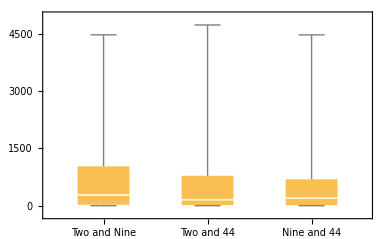

```mathematica
BoxWhiskerChart[{TwoNine,TwoFourtyFour,NineFourtyFour},ChartLabels-> {"Two and Nine","Two and 44","Nine and 44"}]
```

```mathematica
SmoothHistogram[{TwoNine,TwoFourtyFour,NineFourtyFour},{500},ChartLegends->{"Two and Nine","Two and 44","Nine and 44"} ,Frame->True,FrameLabel->{"Distance between sheep","Frequency"}]
```

```mathematica
Histogram[{TwoNine,TwoFourtyFour,NineFourtyFour},{500},ChartLegends->{"Two and Nine","Two and 44","Nine and 44"} ,Frame->True,FrameLabel->{"Distance between sheep","Frequency"}]
```

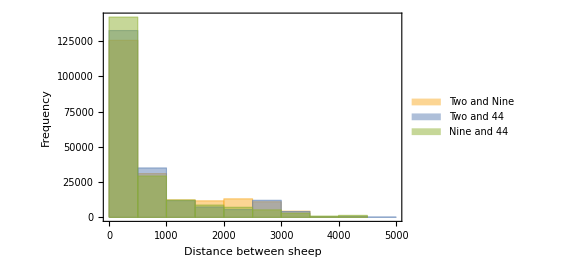
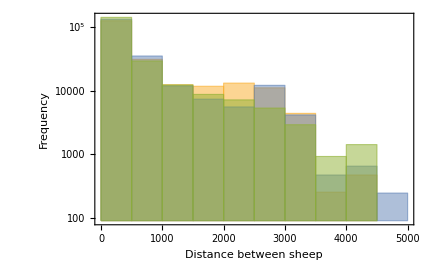

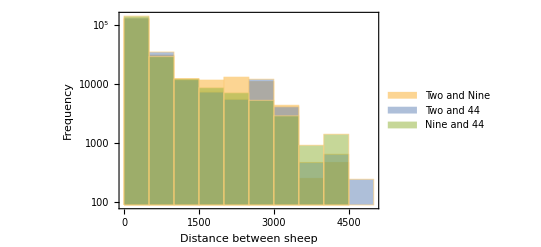

```mathematica
Histogram[{TwoNine,TwoFourtyFour,NineFourtyFour},{500},ChartLegends->{"Two and Nine","Two and 44","Nine and 44"} ,Frame->True,FrameLabel->{"Distance between sheep","Frequency"},ScalingFunctions->"Log"]
```

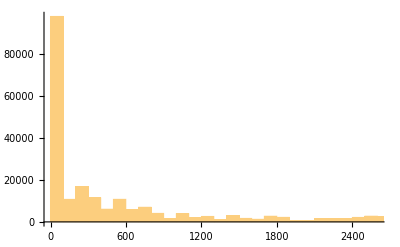

```mathematica
Histogram[fourtyFourFiftyOne,{100}]
```

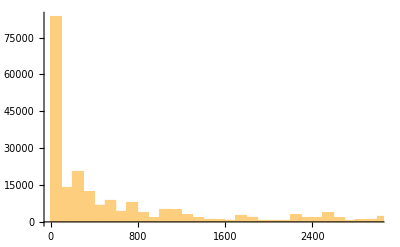

```mathematica
Histogram[threeFiftyOne,{100}]
```

```mathematica
ResourceFunction["StatisticsSummary"][Transpose[{threeFiftyOne,fourtyFourFiftyOne}]]
```

#### All sheep

```mathematica
distance[a_,b_]:=Table[If[Count[{rawCoordinates[[a,n]],rawCoordinates[[a,n]]},Missing[],2]==0,EuclideanDistance[rawCoordinates[[b,n]],rawCoordinates[[b,n]]],Missing[]],{n,1,210351}]
```

```mathematica
Grid[Table[With[{dist=DeleteMissing[distance[i,j]]},{Mean[dist],Median[dist]}]
,{i,10},{j,i-1}]]
```

|  |  |  |  |  |  |  | 
{0.,0.} |  |  |  |  |  |  |  | 
{0.,0.} | {0.,0.} |  |  |  |  |  |  | 
{0.,0.} | {0.,0.} | {0.,0.} |  |  |  |  |  | 
{0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} |  |  |  |  | 
{0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} |  |  |  | 
{0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} |  |  | 
{0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} |  | 
{0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} | 
{0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} | {0.,0.} | {0.,0.}